```mathematica
Quit[]
```

```mathematica
SetDirectory["~/Documents/Univ/exptail_GW/math"];
```

## Mean C

### mono Gauss

```mathematica
sigman[n_,ks_,As_]=ks^n √As
psin[n_,r_,ks_]=Sin[ks r]/(ks r)
```

√As ks^n

Sin[ks r]/(ks r)

```mathematica
gamma1=sigman[1,ks,As]^2/(sigman[0,ks,As]sigman[2,ks,As])
gamma2=sigman[2,ks,As]^2/(sigman[0,ks,As]sigman[4,ks,As])
gamma3=sigman[3,ks,As]^2/(sigman[2,ks,As]sigman[4,ks,As])
Rb[ks_]=√3 sigman[3,ks,As]/sigman[4,ks,As]
```

1

1

1

(√3)/ks

```mathematica
zetabar[x_,mu_]=mu Sin[x]/x//Simplify
```

(mu Sin[x])/x

```mathematica
CompactC[x_,mu_]=2/3(1-(1+x D[zetabar[x,mu], x])^2)//Simplify
```

(2 (x^2-(x+mu x Cos[x]-mu Sin[x])^2))/(3 x^2)

```mathematica
rmcond1[x_]=-x^2/mu(D[zetabar[x,mu], x]+x D[D[zetabar[x,mu], x], x])//Simplify
```

x Cos[x]+(-1+x^2) Sin[x]

```mathematica
rmcond2[x_,mu_]=(1+x D[zetabar[x,mu], x])//Simplify
```

1+mu Cos[x]-(mu Sin[x])/x

```mathematica
xm=x/.FindRoot[rmcond1[x]==0,{x,3}]
```

2.74371

```mathematica
Rarea[x_,mu_]=E^zetabar[x,mu] x
```

ⅇ^((mu Sin[x])/x) x

```mathematica
rmcond2minList=Table[{mu,FindMinimum[rmcond2[x,mu],{x,2.7}][[1]]},{mu,0.9,1,10^-2}];
```

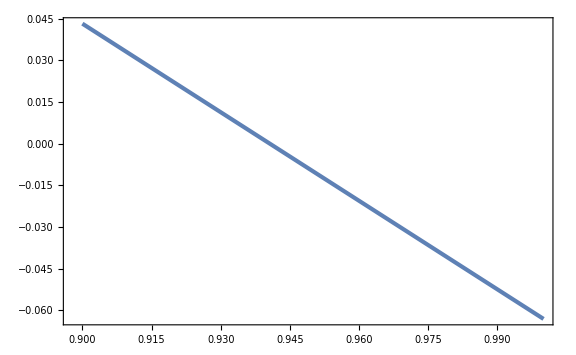

```mathematica
ListPlot[rmcond2minList]
```

```mathematica
rmcond2minint[mu_]=Interpolation[rmcond2minList][mu];
```

```mathematica
mutype2=mu/.FindRoot[rmcond2minint[mu]==0,{mu,0.94}]
```

0.940642

```mathematica
Cx[x_,mu_]=D[CompactC[x,mu], x]//Simplify
Rx[x_,mu_]=D[Rarea[x,mu], x]//Simplify
```

(4 mu (x+mu x Cos[x]-mu Sin[x]) (x Cos[x]+(-1+x^2) Sin[x]))/(3 x^3)

(ⅇ^((mu Sin[x])/x) (x+mu x Cos[x]-mu Sin[x]))/x

```mathematica
VMS[mu_]=(4π)/3 Rarea[xm,mu]^3;
```

```mathematica
Cbarm[mu_]:=1/VMS[mu] 4π NIntegrate[CompactC[x,mu] Rarea[x,mu]^2 D[Rarea[x,mu], x],{x,0,xm}]
```

```mathematica
CbarmList=Table[{mu,Cbarm[mu]},{mu,10^-2,mutype2,10^-2}];
```

```mathematica
Cth=2/5;
```

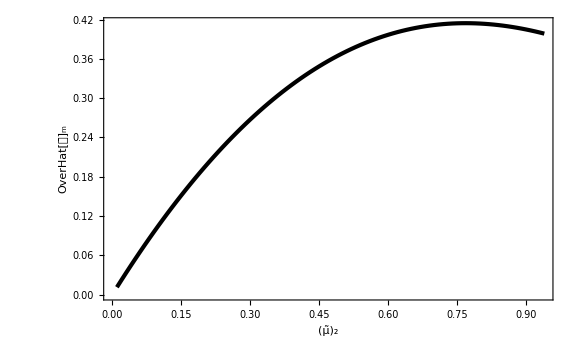

```mathematica
ListPlot[CbarmList,GridLines->{None,{Cth}},FrameLabel->{Subscript[OverTilde[μ], 2],Subscript[OverHat[OverBar[𝒞]], "m"]},PlotStyle->{AbsoluteThickness[3],Black}]
```

```mathematica
Cbarmint[mu_]=Interpolation[CbarmList][mu];
```

```mathematica
muth=mu/.FindRoot[Cbarmint[mu]==Cth,{mu,0.6}][[1]]
```

0.615329

InterpolatingFunction::dmval: Input value {0.000019216} lies outside the range of data in the interpolating function. Extrapolation will be used.

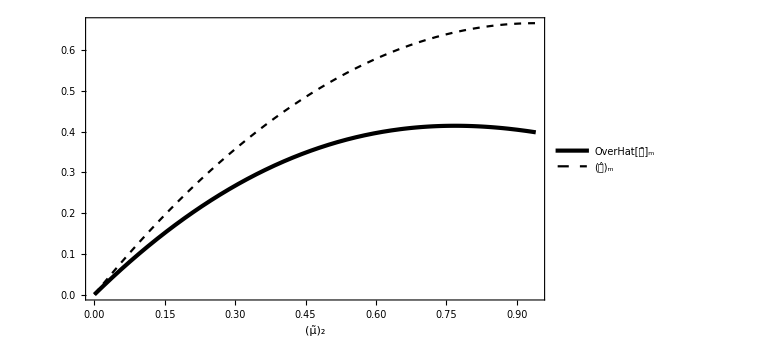

```mathematica
Plot[{Cbarmint[mu],CompactC[xm,mu]},{mu,0,mutype2},GridLines->{{muth},{Cth}},FrameLabel->{Subscript[OverTilde[μ], 2],None},PlotStyle->{{AbsoluteThickness[3],Black},{Black,Dashed}},PlotLegends->Placed[{Subscript[OverHat[OverBar[𝒞]], "m"],Subscript[OverHat[𝒞], "m"]},{0.83,0.2}]]
```

```mathematica
dth=CompactC[xm,muth]
```

0.586929

```mathematica
W[r_]=1/π 4π Integrate[Sin[k rp]^2/k^2,{rp,0,r}]//Simplify
```

(2 k r-Sin[2 k r])/k^3

```mathematica
alpha[mu_]=KK(mu-muth)^γ/.{KK->1,γ->0.36};
```

```mathematica
MoMks[mu_]=xm^2 Exp[2zetabar[xm,mu]]alpha[mu]
dLogMdmu[mu_]=D[Log[MoMks[mu]], mu]//Simplify
```

7.52793 ⅇ^(0.282443 mu) (-0.615329+mu)^0.36

0.282443+0.36/(-0.615329+mu)^1.

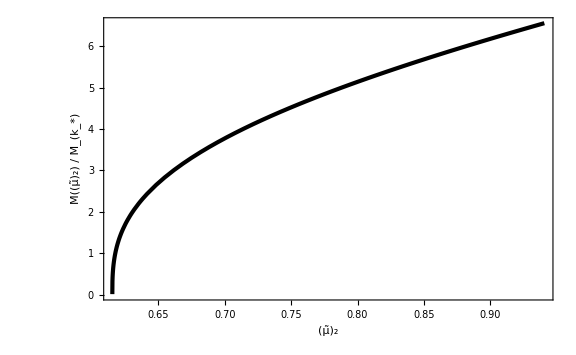

```mathematica
Plot[MoMks[mu],{mu,muth,mutype2},FrameLabel->{Subscript[OverTilde[μ], 2],Row[{M[Subscript[OverTilde[μ], 2]]," / ",Subscript[M, SubStar[k]]}]},PlotStyle->{AbsoluteThickness[3],Black}]
```

```mathematica
f[z_]=1/2 z(z^2-3)(Erf[1/2 √(5/2)z]+Erf[√(5/2)z])+√(2/(5π))((8/5+31/4 z^2)Exp[-5/8 z^2]+(-8/5+1/2 z^2)Exp[-5/2 z^2]);
```

```mathematica
gineV=(1.783 10^-33)^-1;
MpcinvineV=(10^6 3.086 10^16)^-1 1.973 10^-7;
KineV=(1.16 10^4)^-1;
MplineV=2.435 10^(18+9);
kminvsinvMpcineV=(10^3 6.582 10^-16)/(3.086 10^16 10^6);
keq=0.07 0.143
```

0.01001

```mathematica
((10^20 gineV(3/(2π))^(3/2)(1.56 10^13 MpcinvineV)^3)/(0.12 3 MplineV^2(100 kminvsinvMpcineV)^2))^-1
```

5.28928×10^-16

```mathematica
PG[x_,sg2_]=1/(√(2π sg2))Exp[-x^2/(2sg2)];
```

```mathematica
fPBH[Mks_,ks_,As_,mu_]=Mks/10^20 MoMks[mu](ks/(1.56 10^13))^3(f[mu/(√As)]PG[mu,As])/(5.3 10^-16)Abs[dLogMdmu[mu]]^-1 UnitStep[mu-muth];
```

```mathematica
fPBHList=Flatten[ParallelTable[{MoMks[muth+10^logmu],10^logA,fPBH[10^22,1.56 10^12,10^logA,muth+10^logmu]//Quiet},{logmu,-10,Log10[mutype2-muth],10^-2},{logA,-3,0,10^-2}],1];//AbsoluteTiming
```

{9.28041,Null}

```mathematica
Export["fPBH_Gauss.dat",fPBHList];
```

```mathematica
fPBHList=Import["fPBH_Gauss.dat"]//ToExpression;
```

```mathematica
fPBHint[M_,A_]=Interpolation[fPBHList][M,A]UnitStep[MoMks[mutype2]-M,M-MoMks[muth+10^-10]];
```

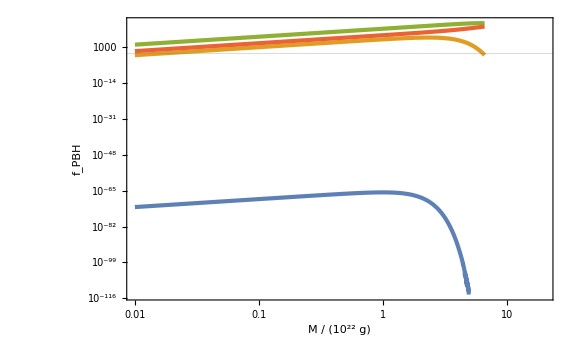

```mathematica
LogLogPlot[{fPBHint[M,10^-3],fPBHint[M,10^-2],fPBHint[M,10^-1],fPBHint[M,1]},{M,0.01,20},GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^22 g)"}],Subscript[f, PBH]},PlotRange->Full]
```

```mathematica
fPBHAList=ParallelTable[{10^logA,NIntegrate[fPBHint[E^logM,10^logA],{logM,Log[10^-2],Log[10]}]},{logA,-3,0,10^-2}];//AbsoluteTiming
```

{7.36184,Null}

```mathematica
Export["fPBHA_Gauss.dat",fPBHAList];
```

```mathematica
fPBHAList=Import["fPBHA_Gauss.dat"]//ToExpression;
```

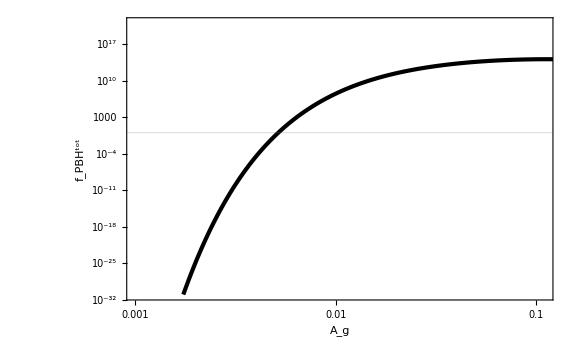

```mathematica
ListLogLogPlot[fPBHAList,FrameLabel->{Subscript[A, g],Subscript[f, PBH]^tot},PlotRange->{{10^-3,1.1 10^-1},{10^-31,10^21}},GridLines->{None,{1}},PlotStyle->{AbsoluteThickness[3],Black}]
```

```mathematica
fPBHAint[A_]=Interpolation[fPBHAList][A];
```

```mathematica
A1=A/.FindRoot[fPBHAint[A]==1,{A,0.005}]
```

0.00517409

```mathematica
Export["fPBHint_Gauss.wdx",fPBHint[M,A1]];
```

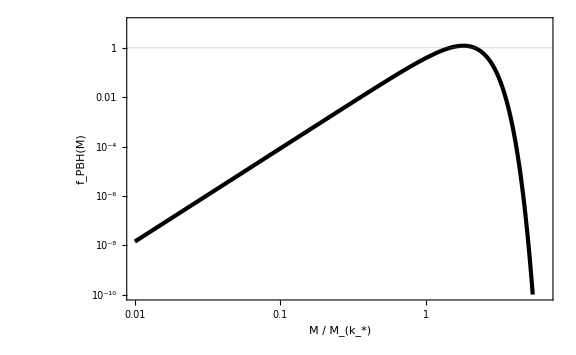

```mathematica
LogLogPlot[fPBHint[M,A1],{M,0.01,MoMks[mutype2]},GridLines->{None,{1}},FrameLabel->{Row[{M," / ",Subscript[M, SubStar[k]]}],Subscript[f, PBH][M]},PlotRange->{10^-10,10},PlotStyle->{AbsoluteThickness[3],Black}]
```

```mathematica
fPBHA1[M_]=Import["fPBHint_Gauss.wdx"];
```

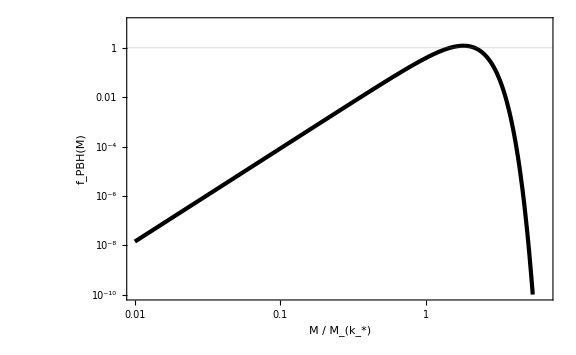

```mathematica
LogLogPlot[fPBHA1[M],{M,0.01,10},GridLines->{None,{1}},FrameLabel->{Row[{M," / ",Subscript[M, SubStar[k]]}],Subscript[f, PBH][M]},PlotRange->{10^-10,10},PlotStyle->{AbsoluteThickness[3],Black}]
```

### mono fNL

```mathematica
sigman[n_,ks_,As_]=ks^n √As
psin[n_,r_,ks_]=Sin[ks r]/(ks r)
```

√As ks^n

Sin[ks r]/(ks r)

```mathematica
gamma1=sigman[1,ks,As]^2/(sigman[0,ks,As]sigman[2,ks,As])
gamma2=sigman[2,ks,As]^2/(sigman[0,ks,As]sigman[4,ks,As])
gamma3=sigman[3,ks,As]^2/(sigman[2,ks,As]sigman[4,ks,As])
Rb[ks_]=√3 sigman[3,ks,As]/sigman[4,ks,As]
```

1

1

1

(√3)/ks

```mathematica
zetaGx[x_,mu_]=mu Sin[x]/x//Simplify
```

(mu Sin[x])/x

```mathematica
zetabar[x_,mu_,fNL_]=zetaGx[x,mu]+3/5 fNL zetaGx[x,mu]^2//Simplify
```

(mu Sin[x] (5 x+3 fNL mu Sin[x]))/(5 x^2)

```mathematica
CompactC[x_,mu_,fNL_]=2/3(1-(1+x D[zetabar[x,mu,fNL], x])^2)//FullSimplify
```

2/3 (1-((5 x^2+mu (x Cos[x]-Sin[x]) (5 x+6 fNL mu Sin[x]))^2)/(25 x^4))

```mathematica
rmcond[x_,mu_,fNL_]=-(5 x^20)/mu(D[zetabar[x,mu,fNL], x]+x D[D[zetabar[x,mu,fNL], x], x])//Simplify
```

x^17 (-6 fNL mu+5 x^2 Cos[x]-6 fNL mu (-1+x^2) Cos[2 x]-5 x Sin[x]+5 x^3 Sin[x]+9 fNL mu x Sin[2 x])

```mathematica
rmcond2[x_,mu_,fNL_]=1/x(1+x D[zetabar[x,mu,fNL], x])//Simplify
```

(5 x^2-5 mu x Sin[x]-6 fNL mu^2 Sin[x]^2+mu x Cos[x] (5 x+6 fNL mu Sin[x]))/(5 x^3)

```mathematica
rmcond2minList=Flatten[ParallelTable[{fNL,mu,FindMinimum[{rmcond2[x,mu,fNL],0<x<5},{x,3}][[1]]},{fNL,-4.1,4.1,10^-2},{mu,0.5,1.1,10^-2}],1];//AbsoluteTiming
```

{179.725,Null}

```mathematica
Export["rmcond2min_fNL.dat",rmcond2minList];
```

```mathematica
rmcond2minList=Import["rmcond2min_fNL.dat"]//ToExpression;
```

```mathematica
ListContourPlot[rmcond2minList]
```

-Graphics-

```mathematica
rmcond2minint[fNL_,mu_]=Interpolation[rmcond2minList][fNL,mu];
```

```mathematica
mu2List=Table[{fNL,mu/.FindRoot[rmcond2minint[fNL,mu]==0,{mu,0.8}]},{fNL,-4.1,4.1,10^-2}];
```

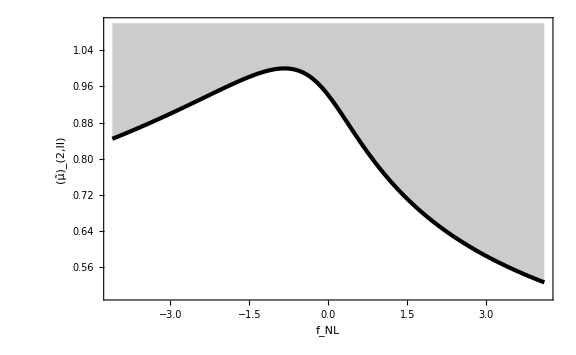

```mathematica
ListPlot[mu2List,PlotStyle->{AbsoluteThickness[3],Black},Filling->Top,FrameLabel->{Subscript[f, NL],Subscript[OverTilde[μ], 2,II]},PlotRange->{0.5,1.1}]
```

```mathematica
mu2int[fNL_]=Interpolation[mu2List][fNL];
```

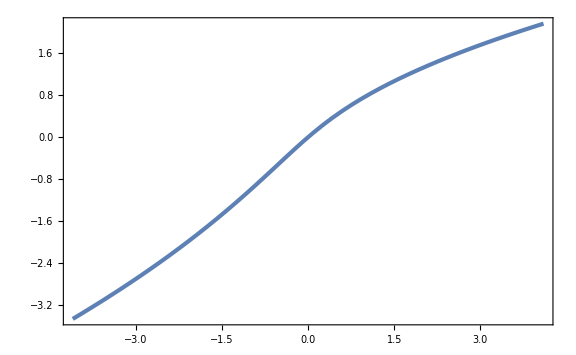

```mathematica
Plot[mu2int[fNL]fNL,{fNL,-4.1,4.1},GridLines->{None,{-5/6}}]
```

```mathematica
xmList=Table[{mufNL,x/.FindRoot[rmcond[x,1,mufNL]==0,{x,3.7}]},{mufNL,-5,5,10^-2}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

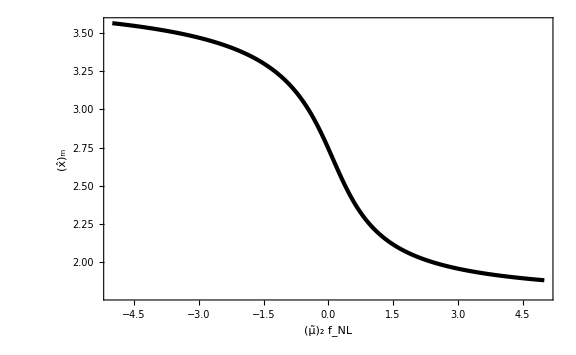

```mathematica
ListPlot[xmList,FrameLabel->{Subscript[OverTilde[μ], 2] Subscript[f, NL],Subscript[OverHat[x], "m"]},PlotStyle->{AbsoluteThickness[3],Black}]
```

```mathematica
xmint[mufNL_]=Interpolation[xmList][mufNL];
```

```mathematica
Rarea[x_,mu_,fNL_]=E^zetabar[x,mu,fNL] x;
```

```mathematica
VMS[mu_,fNL_]=(4π)/3 Rarea[xmint[mu fNL],mu,fNL]^3;
```

```mathematica
Cbarm[mu_,fNL_]:=1/VMS[mu,fNL] 4π NIntegrate[CompactC[x,mu,fNL] Rarea[x,mu,fNL]^2 D[Rarea[x,mu,fNL], x],{x,0,xmint[mu fNL]}]
```

```mathematica
CbarmList=Flatten[ParallelTable[{fNL,mu,Cbarm[mu,fNL]},{fNL,-4.1,4.1,10^-2},{mu,10^-2,1.1,10^-2}],1];//AbsoluteTiming
```

{212.675,Null}

```mathematica
Export["Cbarm_fNL.dat",CbarmList];
```

```mathematica
CbarmList=Import["Cbarm_fNL.dat"]//ToExpression;
```

```mathematica
Cbarmint[fNL_,mu_]=Interpolation[CbarmList][fNL,mu];
```

```mathematica
CbarmmaxList=Table[{fNL,FindMaximum[{Cbarmint[fNL,mu],0<mu<1},{mu,0.4}][[1]]},{fNL,-1,0,10^-2}];
```

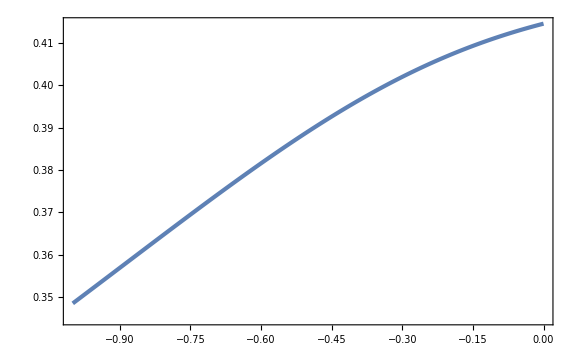

```mathematica
ListPlot[CbarmmaxList,GridLines->{None,{2/5}}]
```

```mathematica
Cbarmmaxint[fNL_]=Interpolation[CbarmmaxList][fNL];
```

```mathematica
fNLmin=fNL/.FindRoot[Cbarmmaxint[fNL]==2/5,{fNL,-0.4}]
```

-0.335546

```mathematica
muthList=Table[{fNL,mu/.FindRoot[Cbarmint[fNL,mu]==2/5,{mu,0.4}]},{fNL,fNLmin,4.1,10^-2}];
```

```mathematica
Plotmuthint[fNL_]=10UnitStep[fNLmin-fNL]+Interpolation[muthList][fNL]UnitStep[fNL-fNLmin];
```

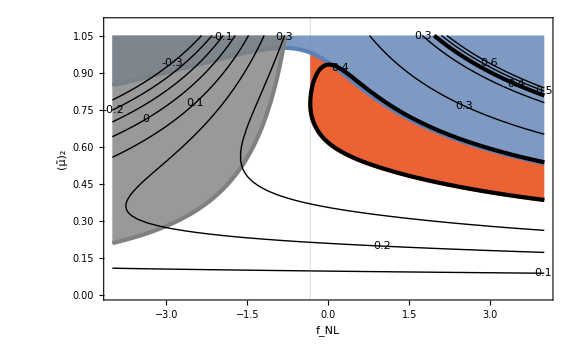

```mathematica
Show[Plot[{mu2int[fNL],Plotmuthint[fNL]},{fNL,fNLmin,4},Filling->{2->{1}},PlotStyle->{None,{AbsoluteThickness[3],Color[4]}},FillingStyle->Opacity[1],AxesOrigin->{-5,-5},PlotRange->{0,1.05},GridLines->{{fNLmin},None}],Plot[mu2int[fNL],{fNL,-4,4},Filling->Top,FillingStyle->Opacity[0.8],PlotRange->{0,1.05}],Plot[-5/(6fNL),{fNL,-4,0},PlotRange->{0,1.05},Filling->Top,PlotStyle->{AbsoluteThickness[3],Gray},FillingStyle->Opacity[0.8],PlotRange->{0,1.05}],ContourPlot[Cbarmint[fNL,mu],{fNL,-4,4},{mu,10^-2,1.05},MaxRecursion->3,Contours->{-0.3,-0.2,-0.1,0,0.1,0.2,0.3,0.4,0.5,0.6},ContourStyle->{Automatic,Automatic,Automatic,Automatic,Automatic,Automatic,Automatic,AbsoluteThickness[3],Automatic,Automatic},ContourShading->None,ContourLabels->(Text[Style[#3,FontFamily->"Palatino",Larger,Background->White],{#1,#2}]&)],PlotRange->{{-4,4},{0,1.1}},FrameLabel->{Subscript[f, NL],Subscript[OverTilde[μ], 2]}]
```

```mathematica
muthint[fNL_]=Interpolation[muthList][fNL];
```

```mathematica
Rareap[x_,mu_,fNL_]=D[Rarea[x,mu,fNL], x]//Simplify;
```

InterpolatingFunction::dmval: Input value {-0.335546,0.0000200342} lies outside the range of data in the interpolating function. Extrapolation will be used.

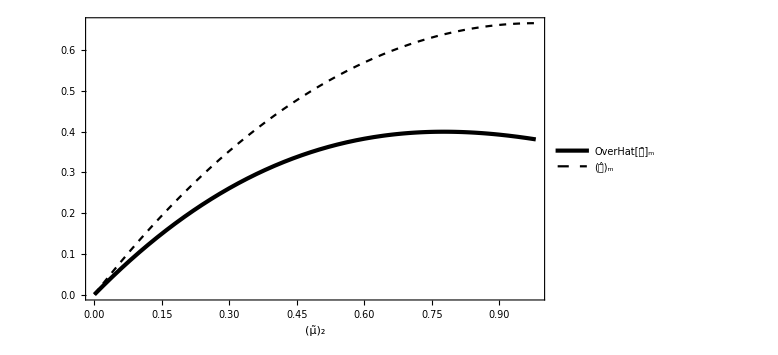

```mathematica
Plot[{Cbarmint[fNLmin,mu],CompactC[xmint[mu fNLmin],mu,fNLmin]},{mu,0,mu2int[fNLmin]},PlotStyle->{{AbsoluteThickness[3],Black},{Dashed,Black}},FrameLabel->{{None,None},{Subscript[OverTilde[μ], 2],Subscript[f, NL]==fNLmin}},PlotLegends->Placed[{Subscript[OverHat[OverBar[𝒞]], "m"],Subscript[OverHat[𝒞], "m"]},{0.9,0.2}],GridLines->{{muthint[fNLmin]},{2/5}}]
```

```mathematica
alpha[mu_,fNL_]=KK(mu-muthint[fNL])^γ/.{KK->1,γ->0.36};
```

```mathematica
MoMks[mu_,fNL_]=xmint[mu fNL]^2 Exp[2zetabar[xmint[mu fNL],mu,fNL]]alpha[mu,fNL];
dLogMdmu[mu_,fNL_]=D[Log[MoMks[mu,fNL]], mu]//Simplify;
```

```mathematica
PlotMoMks[mu_,fNL_]:=MoMks[mu,fNL]/;(mu≥muthint[fNL]&&mu≤mu2int[fNL])
PlotMoMks[mu_,fNL_]:=None/;(mu<muthint[fNL]||mu>mu2int[fNL])
```

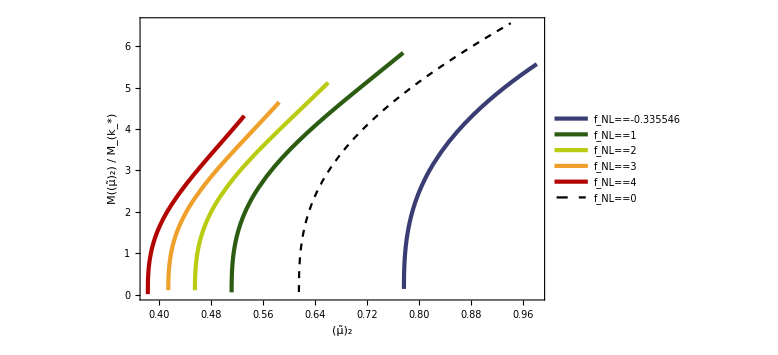

```mathematica
Plot[{PlotMoMks[mu,fNLmin],PlotMoMks[mu,1],PlotMoMks[mu,2],PlotMoMks[mu,3],PlotMoMks[mu,4],PlotMoMks[mu,0]},{mu,muthint[4],mu2int[fNLmin]},FrameLabel->{Subscript[OverTilde[μ], 2],Row[{M[Subscript[OverTilde[μ], 2]]," / ",Subscript[M, Subscript[k, "*"]]}]},PlotStyle->{{AbsoluteThickness[3],ColorData[10,"ColorList"][[9]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[7]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[5]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[3]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[1]]},{Black,Dashed}},PlotLegends->Placed[LineLegend[{Subscript[f, NL]==fNLmin,Subscript[f, NL]==1,Subscript[f, NL]==2,Subscript[f, NL]==3,Subscript[f, NL]==4,Subscript[f, NL]==0},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendLayout->{"Row",2},LegendMarkerSize->20],{0.32,0.87}]]
```

```mathematica
f[z_]=1/2 z(z^2-3)(Erf[1/2 √(5/2)z]+Erf[√(5/2)z])+√(2/(5π))((8/5+31/4 z^2)Exp[-5/8 z^2]+(-8/5+1/2 z^2)Exp[-5/2 z^2]);
```

```mathematica
gineV=(1.783 10^-33)^-1;
MpcinvineV=(10^6 3.086 10^16)^-1 1.973 10^-7;
KineV=(1.16 10^4)^-1;
MplineV=2.435 10^(18+9);
kminvsinvMpcineV=(10^3 6.582 10^-16)/(3.086 10^16 10^6);
keq=0.07 0.143
```

0.01001

```mathematica
((10^20 gineV(3/(2π))^(3/2)(1.56 10^13 MpcinvineV)^3)/(0.12 3 MplineV^2(100 kminvsinvMpcineV)^2))^-1
```

5.28928×10^-16

```mathematica
PG[x_,sg2_]=1/(√(2π sg2))Exp[-x^2/(2sg2)];
```

```mathematica
fPBH[Mks_,ks_,As_,mu_,fNL_]=Mks/10^20 MoMks[mu,fNL](ks/(1.56 10^13))^3(f[mu/(√As)]PG[mu,As])/(5.3 10^-16)Abs[dLogMdmu[mu,fNL]]^-1 UnitStep[mu-muthint[fNL]];
```

```mathematica
(*fPBHListfNLmin=Flatten[ParallelTable[{MoMks[muthint[fNLmin]+10^logmu,fNLmin],10^logA,fPBH[10^20,1.56 10^13,10^logA,muthint[fNLmin]+10^logmu,fNLmin]//Quiet},{logmu,-10,Log10[mu2int[fNLmin]-muthint[fNLmin]],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
fPBHListfNL0=Flatten[ParallelTable[{MoMks[muthint[0]+10^logmu,0],10^logA,fPBH[10^20,1.56 10^13,10^logA,muthint[0]+10^logmu,0]//Quiet},{logmu,-10,Log10[mu2int[0]-muthint[0]],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
fPBHListfNL1=Flatten[ParallelTable[{MoMks[muthint[1]+10^logmu,1],10^logA,fPBH[10^20,1.56 10^13,10^logA,muthint[1]+10^logmu,1]//Quiet},{logmu,-10,Log10[mu2int[1]-muthint[1]],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
fPBHListfNL2=Flatten[ParallelTable[{MoMks[muthint[2]+10^logmu,2],10^logA,fPBH[10^20,1.56 10^13,10^logA,muthint[2]+10^logmu,2]//Quiet},{logmu,-10,Log10[mu2int[2]-muthint[2]],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
fPBHListfNL3=Flatten[ParallelTable[{MoMks[muthint[3]+10^logmu,3],10^logA,fPBH[10^20,1.56 10^13,10^logA,muthint[3]+10^logmu,3]//Quiet},{logmu,-10,Log10[mu2int[3]-muthint[3]],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
fPBHListfNL4=Flatten[ParallelTable[{MoMks[muthint[4]+10^logmu,4],10^logA,fPBH[10^20,1.56 10^13,10^logA,muthint[4]+10^logmu,4]//Quiet},{logmu,-10,Log10[mu2int[4]-muthint[4]],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming*)
```

{23.9441,Null}

{24.3187,Null}

{23.9745,Null}

{23.6201,Null}

{23.5094,Null}

{23.4691,Null}

```mathematica
fPBHListfNL52=Flatten[ParallelTable[{MoMks[muthint[5/2]+10^logmu,5/2],10^logA,fPBH[10^22,1.56 10^12,10^logA,muthint[5/2]+10^logmu,5/2]//Quiet},{logmu,-10,Log10[mu2int[5/2]-muthint[5/2]],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
```

{29.076,Null}

```mathematica
(*Export["fPBHfNLmin.dat",fPBHListfNLmin];
Export["fPBHfNL0.dat",fPBHListfNL0];
Export["fPBHfNL1.dat",fPBHListfNL1];
Export["fPBHfNL2.dat",fPBHListfNL2];
Export["fPBHfNL3.dat",fPBHListfNL3];
Export["fPBHfNL4.dat",fPBHListfNL4];*)
Export["fPBHfNL52.dat",fPBHListfNL52];
```

```mathematica
(*fPBHListfNLmin=Import["fPBHfNLmin.dat"]//ToExpression;
fPBHListfNL0=Import["fPBHfNL0.dat"]//ToExpression;
fPBHListfNL1=Import["fPBHfNL1.dat"]//ToExpression;
fPBHListfNL2=Import["fPBHfNL2.dat"]//ToExpression;
fPBHListfNL3=Import["fPBHfNL3.dat"]//ToExpression;
fPBHListfNL4=Import["fPBHfNL4.dat"]//ToExpression;*)
fPBHListfNL52=Import["fPBHfNL52.dat"]//ToExpression;
```

```mathematica
(*fPBHintfNLmin[M_,A_]=Interpolation[fPBHListfNLmin][M,A]UnitStep[MoMks[mu2int[fNLmin],fNLmin]-M,M-MoMks[muthint[fNLmin]+10^-10,fNLmin]];
fPBHintfNL0[M_,A_]=Interpolation[fPBHListfNL0][M,A]UnitStep[MoMks[mu2int[0],0]-M,M-MoMks[muthint[0]+10^-10,0]];
fPBHintfNL1[M_,A_]=Interpolation[fPBHListfNL1][M,A]UnitStep[MoMks[mu2int[1],1]-M,M-MoMks[muthint[1]+10^-10,1]];
fPBHintfNL2[M_,A_]=Interpolation[fPBHListfNL2][M,A]UnitStep[MoMks[mu2int[2],2]-M,M-MoMks[muthint[2]+10^-10,2]];
fPBHintfNL3[M_,A_]=Interpolation[fPBHListfNL3][M,A]UnitStep[MoMks[mu2int[3],3]-M,M-MoMks[muthint[3]+10^-10,3]];
fPBHintfNL4[M_,A_]=Interpolation[fPBHListfNL4][M,A]UnitStep[MoMks[mu2int[4],4]-M,M-MoMks[muthint[4]+10^-10,4]];*)
```

```mathematica
fPBHintfNL52[M_,A_]=Interpolation[fPBHListfNL52][M,A]UnitStep[MoMks[mu2int[5/2],5/2]-M,M-MoMks[muthint[5/2]+10^-10,5/2]];
```

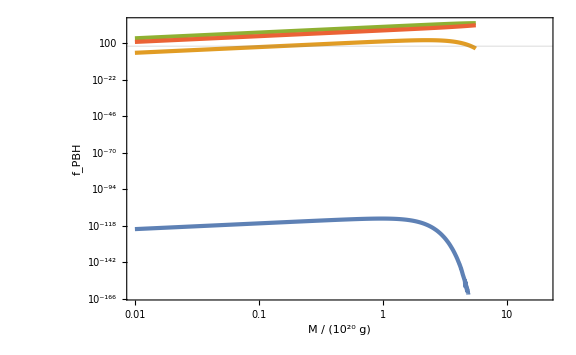

```mathematica
LogLogPlot[{fPBHintfNLmin[M,10^-3],fPBHintfNLmin[M,10^-2],fPBHintfNLmin[M,10^-1],fPBHintfNLmin[M,1]},{M,0.01,20},GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]},PlotRange->Full]
```

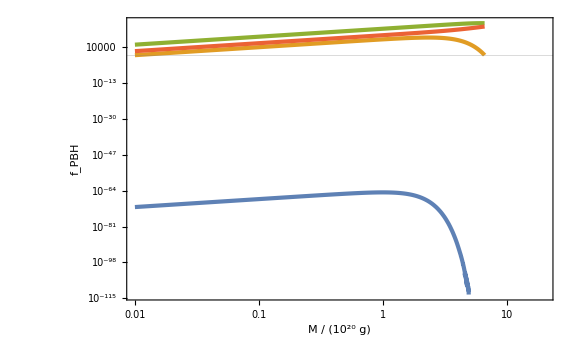

```mathematica
LogLogPlot[{fPBHintfNL0[M,10^-3],fPBHintfNL0[M,10^-2],fPBHintfNL0[M,10^-1],fPBHintfNL0[M,1]},{M,0.01,20},GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]},PlotRange->Full]
```

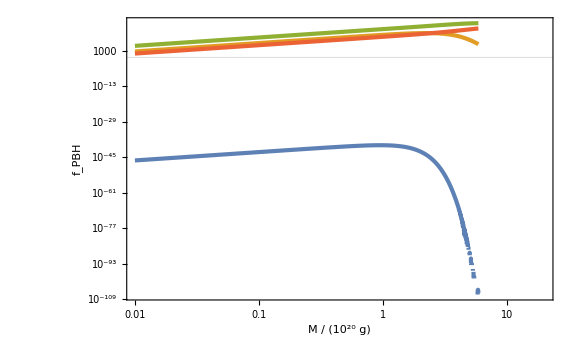

```mathematica
LogLogPlot[{fPBHintfNL1[M,10^-3],fPBHintfNL1[M,10^-2],fPBHintfNL1[M,10^-1],fPBHintfNL1[M,1]},{M,0.01,20},GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]},PlotRange->Full]
```

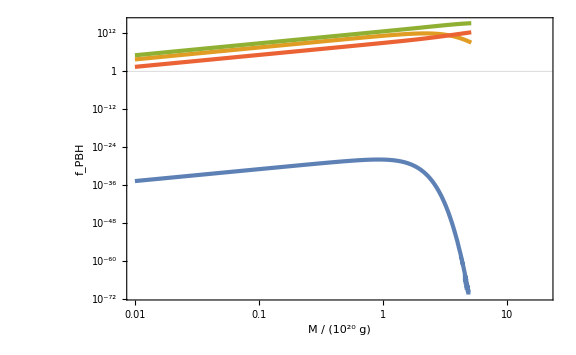

```mathematica
LogLogPlot[{fPBHintfNL2[M,10^-3],fPBHintfNL2[M,10^-2],fPBHintfNL2[M,10^-1],fPBHintfNL2[M,1]},{M,0.01,20},GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]},PlotRange->Full]
```

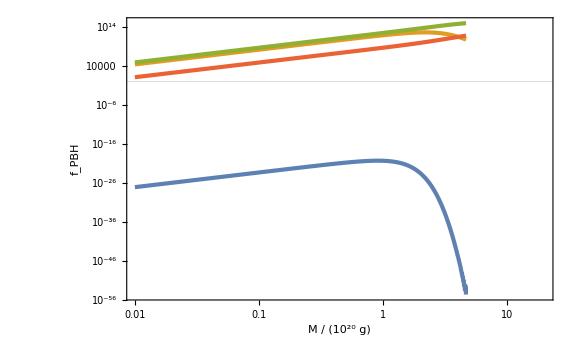

```mathematica
LogLogPlot[{fPBHintfNL3[M,10^-3],fPBHintfNL3[M,10^-2],fPBHintfNL3[M,10^-1],fPBHintfNL3[M,1]},{M,0.01,20},GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]},PlotRange->Full]
```

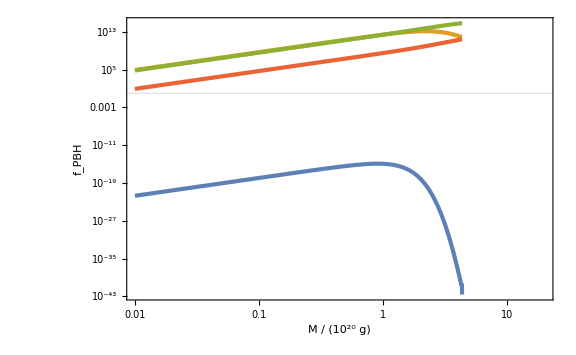

```mathematica
LogLogPlot[{fPBHintfNL4[M,10^-3],fPBHintfNL4[M,10^-2],fPBHintfNL4[M,10^-1],fPBHintfNL4[M,1]},{M,0.01,20},GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]},PlotRange->Full]
```

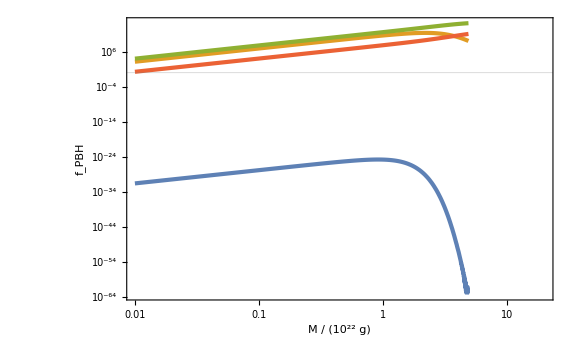

```mathematica
LogLogPlot[{fPBHintfNL52[M,10^-3],fPBHintfNL52[M,10^-2],fPBHintfNL52[M,10^-1],fPBHintfNL52[M,1]},{M,0.01,20},GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^22 g)"}],Subscript[f, PBH]},PlotRange->Full]
```

```mathematica
(*fPBHAListfNLmin=ParallelTable[{10^logA,NIntegrate[fPBHintfNLmin[E^logM,10^logA],{logM,Log[10^-2],Log[10]}]},{logA,-3,0,10^-2}];//AbsoluteTiming
fPBHAListfNL0=ParallelTable[{10^logA,NIntegrate[fPBHintfNL0[E^logM,10^logA],{logM,Log[10^-2],Log[10]}]},{logA,-3,0,10^-2}];//AbsoluteTiming
fPBHAListfNL1=ParallelTable[{10^logA,NIntegrate[fPBHintfNL1[E^logM,10^logA],{logM,Log[10^-2],Log[10]}]},{logA,-3,0,10^-2}];//AbsoluteTiming
fPBHAListfNL2=ParallelTable[{10^logA,NIntegrate[fPBHintfNL2[E^logM,10^logA],{logM,Log[10^-2],Log[10]}]},{logA,-7/2,0,10^-2}];//AbsoluteTiming
fPBHAListfNL3=ParallelTable[{10^logA,NIntegrate[fPBHintfNL3[E^logM,10^logA],{logM,Log[10^-2],Log[10]}]},{logA,-7/2,0,10^-2}];//AbsoluteTiming
fPBHAListfNL4=ParallelTable[{10^logA,NIntegrate[fPBHintfNL4[E^logM,10^logA],{logM,Log[10^-2],Log[10]}]},{logA,-7/2,0,10^-2}];//AbsoluteTiming*)
```

{7.18489,Null}

{7.28587,Null}

{7.27023,Null}

{8.47924,Null}

{8.48765,Null}

{8.43764,Null}

```mathematica
fPBHAListfNL52=ParallelTable[{10^logA,NIntegrate[fPBHintfNL52[E^logM,10^logA],{logM,Log[10^-2],Log[10]}]//Quiet},{logA,-7/2,0,10^-2}];//AbsoluteTiming
```

{9.70441,Null}

```mathematica
(*Export["fPBHAfNLmin.dat",fPBHAListfNLmin];
Export["fPBHAfNL0.dat",fPBHAListfNL0];
Export["fPBHAfNL1.dat",fPBHAListfNL1];
Export["fPBHAfNL2.dat",fPBHAListfNL2];
Export["fPBHAfNL3.dat",fPBHAListfNL3];
Export["fPBHAfNL4.dat",fPBHAListfNL4];*)
Export["fPBHAfNL52.dat",fPBHAListfNL52];
```

```mathematica
(*fPBHAListfNLmin=Import["fPBHAfNLmin.dat"]//ToExpression;
fPBHAListfNL0=Import["fPBHAfNL0.dat"]//ToExpression;
fPBHAListfNL1=Import["fPBHAfNL1.dat"]//ToExpression;
fPBHAListfNL2=Import["fPBHAfNL2.dat"]//ToExpression;
fPBHAListfNL3=Import["fPBHAfNL3.dat"]//ToExpression;
fPBHAListfNL4=Import["fPBHAfNL4.dat"]//ToExpression;*)
fPBHAListfNL52=Import["fPBHAfNL52.dat"]//ToExpression;
```

```mathematica
ColorData[10,"ColorList"]
```

{RGBColor[0.6980392156862745, 0.01568627450980392, 0.],RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786],RGBColor[0.9372549019607843, 0.6274509803921569, 0.16862745098039217],RGBColor[0.9921568627450981, 0.8156862745098039, 0.49019607843137253],RGBColor[0.7254901960784313, 0.8, 0.07058823529411765],RGBColor[0.3176470588235294, 0.49019607843137253, 0.0784313725490196],RGBColor[0.17254901960784313, 0.3607843137254902, 0.07058823529411765],RGBColor[0.3607843137254902, 0.40784313725490196, 0.5333333333333333],RGBColor[0.22745098039215686, 0.23921568627450981, 0.45098039215686275],RGBColor[0.09803921568627451, 0.06666666666666667, 0.25098039215686274],RGBColor[0.5607843137254902, 0.5254901960784314, 0.5647058823529412]}

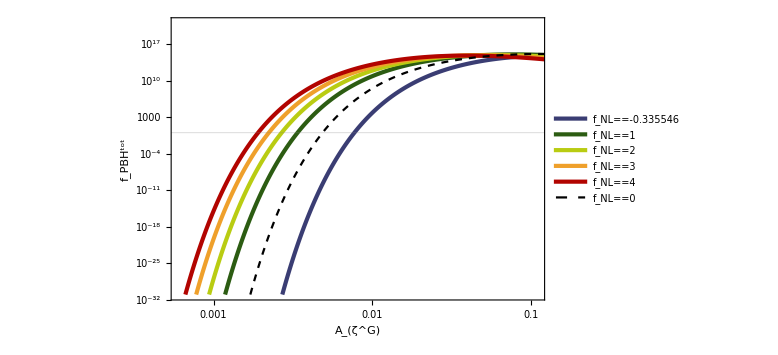

```mathematica
ListLogLogPlot[{fPBHAListfNLmin,fPBHAListfNL1,fPBHAListfNL2,fPBHAListfNL3,fPBHAListfNL4,fPBHAListfNL0},FrameLabel->{Subscript[A, ζ^("G")],Subscript[f, PBH]^tot},PlotRange->{{6 10^-4,1.1 10^-1},{10^-31,10^21}},GridLines->{None,{1}},PlotStyle->{{AbsoluteThickness[3],ColorData[10,"ColorList"][[9]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[7]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[5]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[3]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[1]]},{Black,Dashed}},PlotLegends->Placed[LineLegend[{Subscript[f, NL]==fNLmin,Subscript[f, NL]==1,Subscript[f, NL]==2,Subscript[f, NL]==3,Subscript[f, NL]==4,Subscript[f, NL]==0},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendLayout->{"Column",2},LegendMarkerSize->20],{0.7,0.2}]]
```

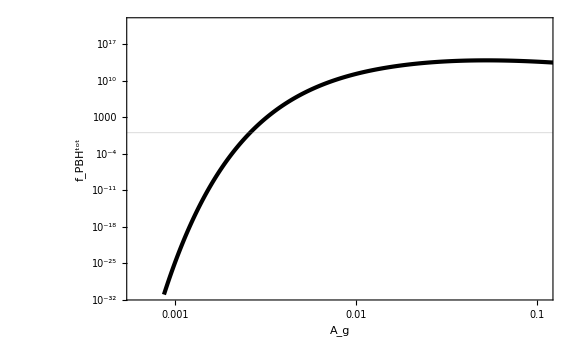

```mathematica
ListLogLogPlot[fPBHAListfNL52,FrameLabel->{{Subscript[f, PBH]^tot,None},{Subscript[A, g],Subscript[f, NL]==5/2}},PlotRange->{{0.6 10^-3,1.1 10^-1},{10^-31,10^21}},GridLines->{None,{1}},PlotStyle->{AbsoluteThickness[3],Black}]
```

```mathematica
(*fPBHAintfNLmin[A_]=Interpolation[fPBHAListfNLmin][A];
fPBHAintfNL0[A_]=Interpolation[fPBHAListfNL0][A];
fPBHAintfNL1[A_]=Interpolation[fPBHAListfNL1][A];
fPBHAintfNL2[A_]=Interpolation[fPBHAListfNL2][A];
fPBHAintfNL3[A_]=Interpolation[fPBHAListfNL3][A];
fPBHAintfNL4[A_]=Interpolation[fPBHAListfNL4][A];*)
```

```mathematica
fPBHAintfNL52[A_]=Interpolation[fPBHAListfNL52][A];
```

```mathematica
(*A1fNLmin=A/.FindRoot[Log10[fPBHAintfNLmin[A]]==0,{A,0.005}]
A1fNL0=A/.FindRoot[Log10[fPBHAintfNL0[A]]==0,{A,0.005}]
A1fNL1=A/.FindRoot[Log10[fPBHAintfNL1[A]]==0,{A,0.003}]
A1fNL2=A/.FindRoot[Log10[fPBHAintfNL2[A]]==0,{A,0.003}]
A1fNL3=A/.FindRoot[Log10[fPBHAintfNL3[A]]==0,{A,0.003}]
A1fNL4=A/.FindRoot[Log10[fPBHAintfNL4[A]]==0,{A,0.003}]*)
```

0.00771511

0.00486276

0.00338132

0.00268592

0.00222991

0.00190794

```mathematica
A1fNL52=A/.FindRoot[Log10[fPBHAintfNL52[A]]==0,{A,0.003}]
```

0.00259432

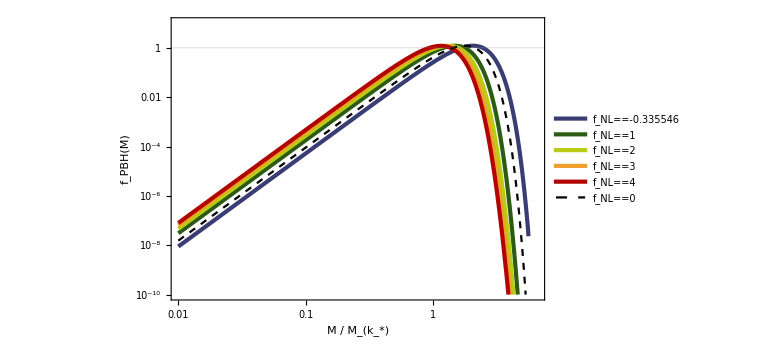

```mathematica
LogLogPlot[{fPBHintfNLmin[M,A1fNLmin],fPBHintfNL1[M,A1fNL1],fPBHintfNL2[M,A1fNL2],fPBHintfNL3[M,A1fNL3],fPBHintfNL4[M,A1fNL4],fPBHintfNL0[M,A1fNL0]},{M,0.01,10},GridLines->{None,{1}},FrameLabel->{Row[{M," / ",Subscript[M, SubStar[k]]}],Subscript[f, PBH][M]},PlotRange->{10^-10,10},PlotStyle->{{AbsoluteThickness[3],ColorData[10,"ColorList"][[9]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[7]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[5]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[3]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[1]]},{Black,Dashed}},PlotLegends->Placed[LineLegend[{Subscript[f, NL]==fNLmin,Subscript[f, NL]==1,Subscript[f, NL]==2,Subscript[f, NL]==3,Subscript[f, NL]==4,Subscript[f, NL]==0},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendLayout->{"Column",2},LegendMarkerSize->20],{0.6,0.2}]]
```

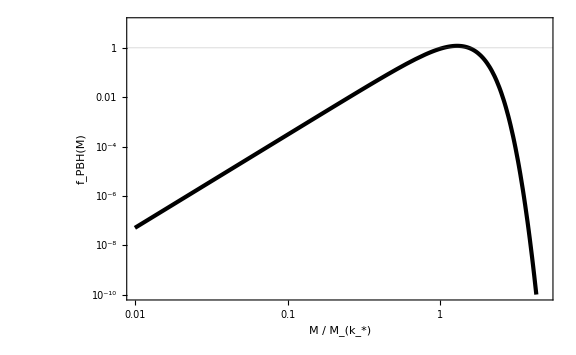

```mathematica
LogLogPlot[fPBHintfNL52[M,A1fNL52],{M,0.01,10},GridLines->{None,{1}},FrameLabel->{{Subscript[f, PBH][M],None},{Row[{M," / ",Subscript[M, SubStar[k]]}],Subscript[f, NL]==5/2}},PlotRange->{10^-10,10},PlotStyle->{AbsoluteThickness[3],Black}]
```

```mathematica
Export["fPBHint_fNL52.wdx",fPBHintfNL52[M,A1fNL52]];
```

```mathematica
fPBHA1fNL52[M_]=Import["fPBHint_fNL52.wdx"];
```

```mathematica
LogLogPlot[fPBHA1fNL52[M],{M,0.01,10},GridLines->{None,{1}},FrameLabel->{{Subscript[f, PBH][M],None},{Row[{M," / ",Subscript[M, SubStar[k]]}],Subscript[f, NL]==5/2}},PlotRange->{10^-10,10},PlotStyle->{AbsoluteThickness[3],Black}]
```

-Graphics-

### mono exp

```mathematica
sigman[n_,ks_,As_]=ks^n √As
psin[n_,r_,ks_]=Sin[ks r]/(ks r)
```

√As ks^n

Sin[ks r]/(ks r)

```mathematica
gamma1=sigman[1,ks,As]^2/(sigman[0,ks,As]sigman[2,ks,As])
gamma2=sigman[2,ks,As]^2/(sigman[0,ks,As]sigman[4,ks,As])
gamma3=sigman[3,ks,As]^2/(sigman[2,ks,As]sigman[4,ks,As])
Rb[ks_]=√3 sigman[3,ks,As]/sigman[4,ks,As]
```

1

1

1

(√3)/ks

```mathematica
zetaGx[x_,mu_]=mu Sin[x]/x//Simplify
```

(mu Sin[x])/x

```mathematica
zetabar[x_,mu_]=-1/3 Log[1-3mu Sin[x]/x]//Simplify
```

-1/3 Log[1-(3 mu Sin[x])/x]

```mathematica
CompactC[x_,mu_]=2/3(1-(1+x D[zetabar[x,mu], x])^2)//Simplify
```

-(2 mu (x Cos[x]-Sin[x]) (2 x+mu x Cos[x]-7 mu Sin[x]))/(3 (x-3 mu Sin[x])^2)

```mathematica
rmcond[x_,mu_]=-1/(mu x^2)(D[zetabar[x,mu], x]+x D[D[zetabar[x,mu], x], x])//Simplify
```

(-3 mu x+(-1+x^2) Sin[x]+Cos[x] (x+3 mu Sin[x]))/(x^2 (x-3 mu Sin[x])^2)

```mathematica
rmcond2[x_,mu_]=(1+x D[zetabar[x,mu], x])//Simplify
```

(x+mu x Cos[x]-4 mu Sin[x])/(x-3 mu Sin[x])

```mathematica
xmList=Sort[Table[{1/3-10^logmu,x/.FindRoot[rmcond[x,1/3-10^logmu]==0,{x,0.1}]},{logmu,-6,Log10[1/3],10^-2}],#1[[1]]<#2[[1]]&];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

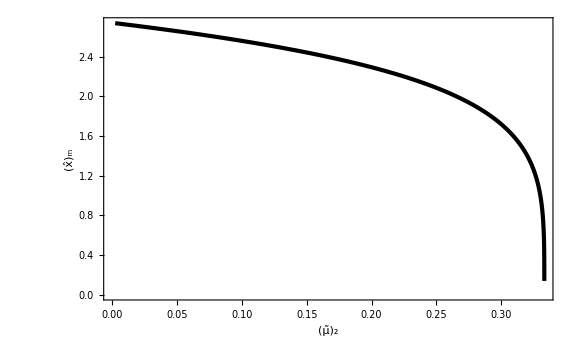

```mathematica
ListPlot[xmList,FrameLabel->{Subscript[OverTilde[μ], 2],Subscript[OverHat[x], "m"]},PlotStyle->{AbsoluteThickness[3],Black},PlotRange->Full]
```

```mathematica
xmint[mu_]=Interpolation[xmList][mu];
```

```mathematica
Rarea[x_,mu_]=E^zetabar[x,mu] x;
```

```mathematica
VMS[mu_]=(4π)/3 Rarea[xmint[mu],mu]^3;
```

```mathematica
Cbarm[mu_]:=1/VMS[mu] 4π NIntegrate[CompactC[x,mu] Rarea[x,mu]^2 D[Rarea[x,mu], x],{x,0,xmint[mu]}]
```

```mathematica
CbarmList=Sort[Table[{1/3-10^logmu,Cbarm[1/3-10^logmu]},{logmu,-6,Log10[1/3],10^-2}],#1[[1]]<#2[[1]]&];//AbsoluteTiming
```

{4.72251,Null}

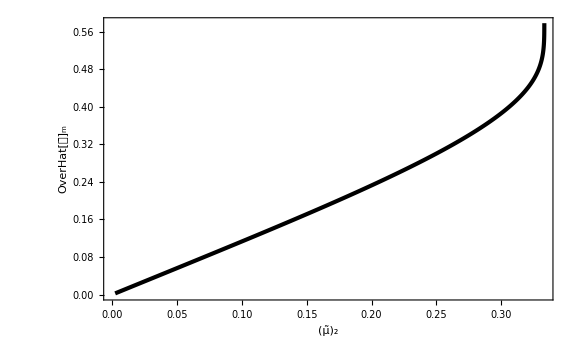

```mathematica
ListPlot[CbarmList,GridLines->{None,{2/5}},PlotRange->Full,FrameLabel->{Subscript[OverTilde[μ], 2],Subscript[OverHat[OverBar[𝒞]], "m"]},PlotStyle->{Black,AbsoluteThickness[3]}]
```

```mathematica
Cbarmint[mu_]=Interpolation[CbarmList][mu];
```

```mathematica
muth=mu/.FindRoot[Cbarmint[mu]==2/5,{mu,0.3}]
```

0.306158

InterpolatingFunction::dmval: Input value {6.80952×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {6.80272×10^-9} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

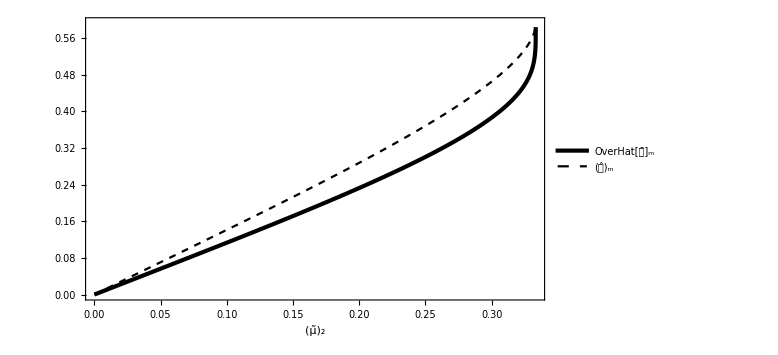

```mathematica
Plot[{Cbarmint[mu],CompactC[xmint[mu],mu]},{mu,0,1/3},PlotStyle->{{AbsoluteThickness[3],Black},{Dashed,Black}},FrameLabel->{
Subscript[OverTilde[μ], 2]},PlotLegends->Placed[{Subscript[OverHat[OverBar[𝒞]], "m"],Subscript[OverHat[𝒞], "m"]},{0.8,0.2}],GridLines->{{muth},{2/5}}]
```

```mathematica
alpha[mu_]=KK(mu-muth)^γ/.{KK->1,γ->0.36};
```

```mathematica
MoMks[mu_]=xmint[mu]^2 Exp[2zetabar[xmint[mu],mu]]alpha[mu];
dLogMdmu[mu_]=D[Log[MoMks[mu]], mu]//Simplify;
```

```mathematica
mumax=mu/.FindMaximum[{MoMks[mu],muth<mu<1/3},{mu,0.33}][[2]]
Mmax=MoMks[mumax]
```

0.325065

0.926411

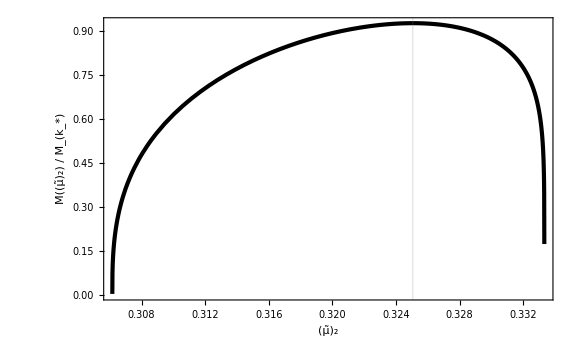

```mathematica
Plot[MoMks[mu],{mu,muth,1/3},FrameLabel->{Subscript[OverTilde[μ], 2],Row[{M[Subscript[OverTilde[μ], 2]]," / ",Subscript[M, SubStar[k]]}]},GridLines->{{mumax},None},PlotStyle->{Black,AbsoluteThickness[3]}]
```

```mathematica
f[z_]=1/2 z(z^2-3)(Erf[1/2 √(5/2)z]+Erf[√(5/2)z])+√(2/(5π))((8/5+31/4 z^2)Exp[-5/8 z^2]+(-8/5+1/2 z^2)Exp[-5/2 z^2]);
```

```mathematica
gineV=(1.783 10^-33)^-1;
MpcinvineV=(10^6 3.086 10^16)^-1 1.973 10^-7;
KineV=(1.16 10^4)^-1;
MplineV=2.435 10^(18+9);
kminvsinvMpcineV=(10^3 6.582 10^-16)/(3.086 10^16 10^6);
keq=0.07 0.143
```

0.01001

```mathematica
((10^20 gineV(3/(2π))^(3/2)(1.56 10^13 MpcinvineV)^3)/(0.12 3 MplineV^2(100 kminvsinvMpcineV)^2))^-1
```

5.28928×10^-16

```mathematica
PG[x_,sg2_]=1/(√(2π sg2))Exp[-x^2/(2sg2)];
```

```mathematica
fPBH[Mks_,ks_,As_,mu_]=Mks/10^20 MoMks[mu](ks/(1.56 10^13))^3(f[mu/(√As)]PG[mu,As])/(5.3 10^-16)Abs[dLogMdmu[mu]]^-1 UnitStep[mu-muth];
```

```mathematica
fPBHlowList=Flatten[ParallelTable[{MoMks[muth+10^logmu],10^logA,fPBH[10^22,1.56 10^12,10^logA,muth+10^logmu]//Quiet},{logmu,-10,Log10[mumax-muth],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
fPBHhighList=Sort[Flatten[ParallelTable[{MoMks[1/3-10^logmu],10^logA,fPBH[10^22,1.56 10^12,10^logA,1/3-10^logmu]//Quiet},{logmu,-6,Log10[1/3-mumax],10^-2},{logA,-4,0,10^-2}],1],#1[[1]]<#2[[1]]&];//AbsoluteTiming
```

$Aborted

$Aborted

```mathematica
Export["fPBHexplow.dat",fPBHlowList];
Export["fPBHexphigh.dat",fPBHhighList];
```

```mathematica
fPBHlowList=Import["fPBHexplow.dat"]//ToExpression;
fPBHhighList=Import["fPBHexphigh.dat"]//ToExpression;
```

```mathematica
fPBHintlow[M_,A_]=Interpolation[fPBHlowList][M,A]UnitStep[MoMks[mumax]-M,M-MoMks[muth]];
fPBHinthigh[M_,A_]=Interpolation[fPBHhighList][M,A]UnitStep[MoMks[mumax]-M,M-MoMks[1/3-10^-6]];
```

InterpolatingFunction::dmval: Input value {0.0100016,1/1000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0116798,1/1000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0136397,1/1000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

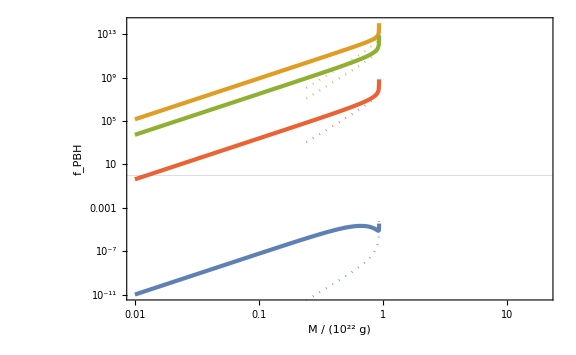

```mathematica
Show[LogLogPlot[{fPBHintlow[M,10^-3],fPBHintlow[M,10^-2],fPBHintlow[M,10^-1],fPBHintlow[M,1]},{M,0.01,20},GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^22 g)"}],Subscript[f, PBH]},PlotRange->Full],LogLogPlot[{fPBHinthigh[M,10^-3],fPBHinthigh[M,10^-2],fPBHinthigh[M,10^-1],fPBHinthigh[M,1]},{M,0.01,20},PlotStyle->Dotted]]
```

```mathematica
fPBHAList=ParallelTable[{10^logA,NIntegrate[fPBHintlow[E^logM,10^logA],{logM,Log[10^-2],0}]//Quiet},{logA,-4,0,10^-2}];//AbsoluteTiming
```

{9.72088,Null}

```mathematica
Export["fPBHA_exp.dat",fPBHAList];
```

```mathematica
fPBHAList=Import["fPBHA_exp.dat"]//ToExpression;
fPBHAListGauss=Import["fPBHA_Gauss.dat"]//ToExpression;
fPBHAfNL52=Import["fPBHAfNL52.dat"]//ToExpression;
```

```mathematica
fPBHAint[A_]=Interpolation[fPBHAList][A];
fPBHAGaussint[A_]=Interpolation[fPBHAListGauss][A];
fPBHAfNL52int[A_]=Interpolation[fPBHAfNL52][A];
```

```mathematica
A1=A/.FindRoot[Log10[fPBHAint[A]]==0,{A,0.001}]
A1Gauss=A/.FindRoot[Log10[fPBHAGaussint[A]]==0,{A,0.001}]
A1fNL52=A/.FindRoot[Log10[fPBHAfNL52int[A]]==0,{A,0.001}]
```

0.00131621

0.00517409

0.00259432

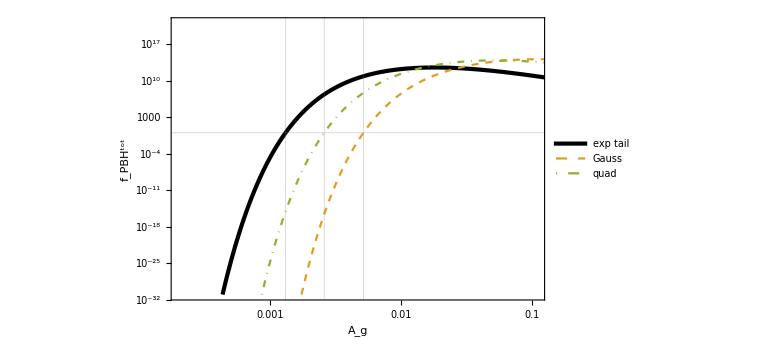

```mathematica
ListLogLogPlot[{fPBHAList,fPBHAListGauss,fPBHAfNL52},FrameLabel->{Subscript[A, g],Subscript[f, PBH]^tot},PlotRange->{{2 10^-4,1.1 10^-1},{10^-31,10^21}},GridLines->{{A1,A1fNL52,A1Gauss},{1}},PlotStyle->{{AbsoluteThickness[3],Black},{Color[1],Dashed},{Color[2],DotDashed}},PlotLegends->Placed[LineLegend[{"exp tail","Gauss","quad"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"](*,LegendLayout->{"Column",2}*),LegendMarkerSize->20],{0.8,0.25}]]
```

```mathematica
fPBHintGauss[M_]=Import["fPBHint_Gauss.wdx"];
fPBHintfNL52[M_]=Import["fPBHint_fNL52.wdx"];
```

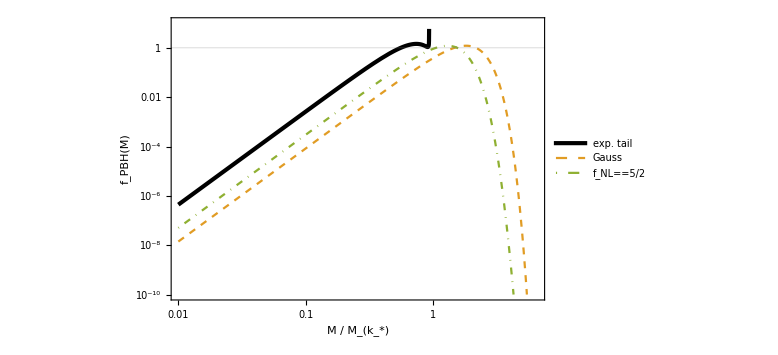

```mathematica
LogLogPlot[{fPBHintlow[M,A1],fPBHintGauss[M],fPBHintfNL52[M]},{M,0.01,10},GridLines->{None,{1}},FrameLabel->{Row[{M," / ",Subscript[M, SubStar[k]]}],Subscript[f, PBH][M]},PlotRange->{10^-10,10},PlotStyle->{{AbsoluteThickness[3],Black},{Color[1],Dashed},{Color[2],DotDashed}},PlotLegends->Placed[LineLegend[{"exp. tail","Gauss",Subscript[f, NL]==5/2},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendLayout->{"Column",2},LegendMarkerSize->20],{0.6,0.2}]]
```

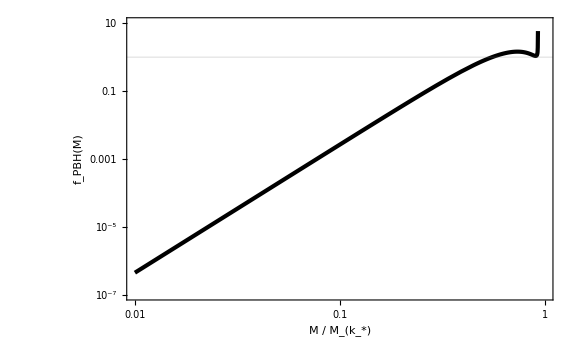

```mathematica
LogLogPlot[fPBHintlow[M,A1],{M,0.01,10},GridLines->{None,{1}},FrameLabel->{{Subscript[f, PBH][M],None},{Row[{M," / ",Subscript[M, SubStar[k]]}],None}},PlotRange->{10^-7,10},PlotStyle->{AbsoluteThickness[3],Black}]
```

```mathematica
Log[0.9]-Log[0.5]
```

0.587787

```mathematica
Mmax
```

0.926411

```mathematica
NIntegrate[fPBHintlow[M,A1]/M,{M,0.01,Mmax}]
```

1.

```mathematica
NIntegrate[fPBHintlow[M,A1]/M,{M,0.8,Mmax}]
```

0.183278

```mathematica
NIntegrate[fPBHintlow[M,A1]/M,{M,0.5,0.8}]
```

0.571568

```mathematica
NIntegrate[fPBHintlow[M,A1]/M,{M,0.01,0.5}]
```

0.245156

```mathematica
18+57+25
```

100

```mathematica
Cos[0.1]
```

0.995004

```mathematica
(0.99-Cos[0.1])^2/Cos[0.1]^2
```

0.0000252938

```mathematica
Evaporation=Join[{{10^14,10^-10}},Import["evaporation.csv"]];
Lensing=Import["lensing.csv"];
```

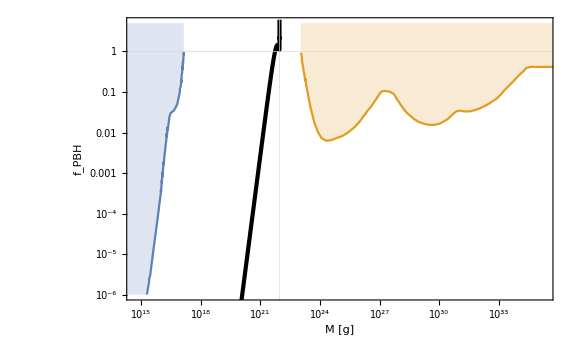

```mathematica
Show[ListLogLogPlot[{Evaporation,Lensing},PlotRange->{{0.5 10^15,2 10^35},{10^-6,5}},Filling->Top,GridLines->{{Mmax 10^22},{1}},FrameLabel->{"M [g]",Subscript[f, PBH]},PlotStyle->Automatic,GridLinesStyle->{{Black,Dashed,AbsoluteThickness[1]},Black}],LogLogPlot[fPBHintlow[M/10^22,A1],{M,10^20,10^22},PlotStyle->{AbsoluteThickness[3],Black}(*,Filling->Bottom*)]]
```